# Lab 3 William Keilsohn Section 32 3/6/2014

Question 1a. Let A be the region bounded by the curves y=e^-x, y=1,and x=2. Generate a plot of the region.

```mathematica
Quit[]
```

```mathematica
f[x_]=Exp[-x]
```

ⅇ^-x

```mathematica
g[x_]=1
```

1

```mathematica
NSolve[f[x]==g[x]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.}}

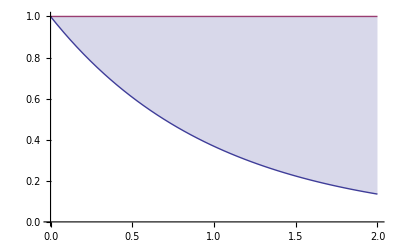

```mathematica
p1=Plot[{f[x],g[x]},{x,0,2},Filling->{1->{2}}]
```

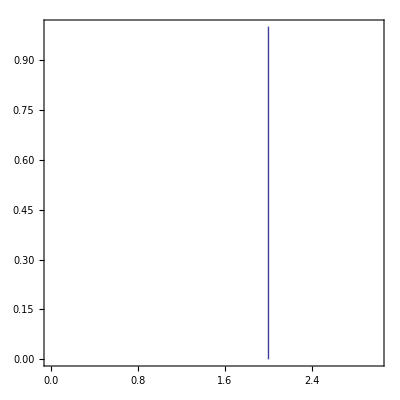

```mathematica
p2=ContourPlot[x==2,{x,0,3},{y,0,1}]
```

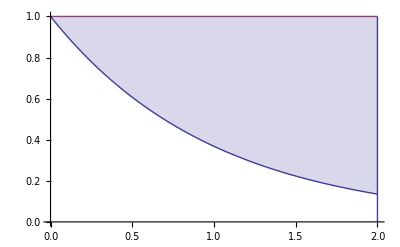

```mathematica
A=Show[{p1,p2}]
```

```mathematica
A
```

-Graphics-

Question 1b. Find the volume obtained by revolving the region A around the line y=2. Exact value and decimal required.

```mathematica
A1=Pi*((2-Exp[-x])^2-(2-1)^2)
```

(-1+(2-ⅇ^-x)^2) π

Washer Method is used.

```mathematica
A2=Integrate[A1,{x,0,2}]
```

((-1+8 ⅇ^2+5 ⅇ^4) π)/(2 ⅇ^4)

```mathematica
N[((-1+8 ⅇ^2+5 ⅇ^4) π)/(2 ⅇ^4)]
```

9.52588

Question 2a. Let A be the region bounded by the curves: y=x+7, and y=9-x^2. Plot region A.

```mathematica
Quit[]
```

```mathematica
f[x_]=x+7
```

7+x

```mathematica
g[x_]=9-x^2
```

9-x^2

```mathematica
NSolve[f[x]==g[x]]
```

{{x→-2.},{x→1.}}

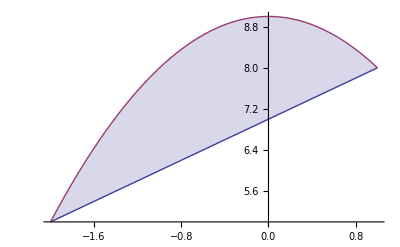

```mathematica
A=Plot[{f[x],g[x]},{x,-2,1},Filling->{1->{2}}]
```

```mathematica
A
```

-Graphics-

Question 2b. Find the volume of A revolved around x=2.

```mathematica
A1=2*Pi*(2-x)*(g[x]-f[x])
```

2 π (2-x) (2-x-x^2)

```mathematica
A2=Integrate[A1,{x,-2,1}]
```

(45 π)/2

```mathematica
N[(45 π)/2]
```

70.6858

Question 3a. Use mathematica to compute and generate plots of A1 and A2.

```mathematica
Quit[]
```

```mathematica
f[x_]=5*x*(1-x)^2
```

5 (1-x)^2 x

```mathematica
g[x_]=8*x^3*(1-x)
```

8 (1-x) x^3

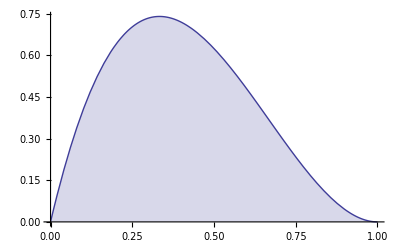

```mathematica
p1=Plot[f[x],{x,0,1},Filling->{1->Axis}]
```

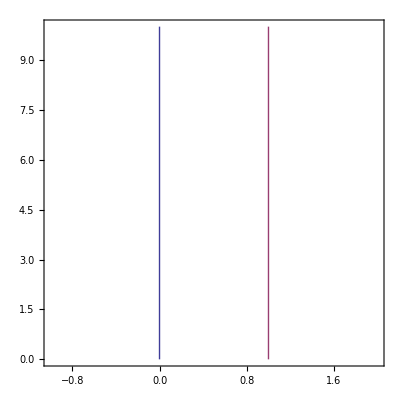

```mathematica
p2=ContourPlot[{x==0,x==1},{x,-1,2},{y,0,10}]
```

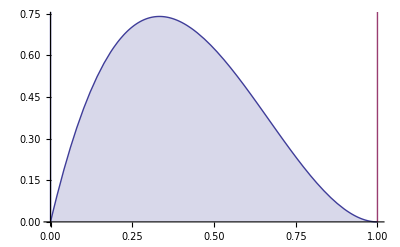

```mathematica
A1=Show[p1,p2]
```

```mathematica
Integrate[f[x],{x,0,1}]
```

5/12

```mathematica
N[5/12]
```

0.416667

```mathematica
g[x]
```

8 (1-x) x^3

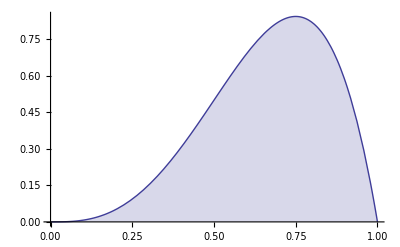

```mathematica
p3=Plot[g[x],{x,0,1},Filling->{1->Axis}]
```

```mathematica
p4=ContourPlot[{x==0,x==1},{x,-1,2},{y,0,10}]
```

-Graphics-

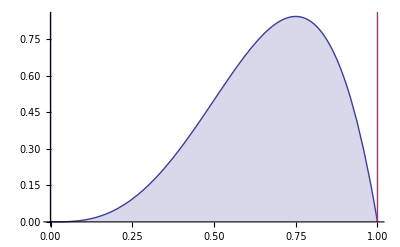

```mathematica
A2=Show[p3,p4]
```

```mathematica
Integrate[g[x],{x,0,1}]
```

2/5

```mathematica
N[2/5]
```

0.4

Therefore, A1 is larger than A2.

Question 3b. Compute the volumes of V1 and V2.

```mathematica
f1[x_]=2*Pi*(1+x)(f[x])
```

10 π (1-x)^2 x (1+x)

```mathematica
V1=Integrate[f1[x],{x,0,1}]
```

(7 π)/6

```mathematica
N[(7 π)/6]
```

3.66519

```mathematica
g2[x_]=2*Pi*(x+1)(g[x])
```

16 π (1-x) x^3 (1+x)

```mathematica
V2=Integrate[g2[x],{x,0,1}]
```

(4 π)/3

```mathematica
N[(4 π)/3]
```

4.18879

Therefore V2 has a larger volume than V1.

Question 3c. Which region produced the larger volume? Why do you think that is?

A: The region with the smaller area produced the larger volume. This was most likely due to the location on the x-axis where the value for y was greatest. The region with the smaller area had its largest y values farthest from x=-1 on the x-axis. This means that when the volume of the solids were calculated using cylindrical shell method, the largest hight vaues were multiplied by the largest radius values. Large numbers multiplied by large numbers tends to produce large numbers. The region with the largest area had its greatest y values near the y-axis and thus closer to x=-1 than the other region. This means that when cylindrical shell method was used, the smallest radius values were multiplied by the largest hight values and visa versa. Large numbers multiplied by small ones tend to produce smaller values than when large numbers are multiplied by large numbers. This is not apparent in the area of the regions because when the integrals were taken to compute the areas of the region no form of radius or third plane was involved.